# MSC602 Comprehensive Report

## Inverse Kinematics of SCORBOT - ER9Pro

Members:
	Bakbergen Yermekbayev 201926481
	Rustem Tnymkulov 201978347
	Yerzhan Akzhigitov 202190319

Course Instructor: 
	Professor Dmitry Sizov

^2

### Problem Statement

We have a 3-link planar robotic arm (SCORBOT-ER9Pro) with link lengths L1, L2, L3 and joint angles θ1, θ2, θ3 (all in degrees).

• Forward Kinematics (FK): Given (θ1, θ2, θ3), compute the end-effector pose (x, y, φ), where φ = θ1 + θ2 + θ3 is the end-effector orientation.
• Inverse Kinematics (IK): Given a target pose (xTarget, yTarget, φTarget), find (θ1, θ2, θ3).

Why a 3×3 Jacobian? With θ3 free, we have 3 unknowns. Position (x, y) alone gives only 2 equations - the system is underdetermined (infinitely many solutions). Adding the orientation φ as a 3rd equation balances unknowns and equations, producing a square 3×3 Jacobian that Newton-Raphson can invert.

The IK problem becomes solving 3 nonlinear equations in 3 unknowns:
    f1(θ1, θ2, θ3) = FK_x - xTarget = 0
    f2(θ1, θ2, θ3) = FK_y - yTarget = 0
    f3(θ1, θ2, θ3) = (θ1+θ2+θ3) - φTarget = 0
    
   
                                 															-Graphics-

#### Physical Constants (SCORBOT-ER9Pro Datasheet)

```mathematica
L1 = 280;  (* mm - upper arm *)
L2 = 230;  (* mm - forearm *)
L3 = 111;  (* mm - hand / gripper *)

θ1Max = 101;  (* shoulder rotation range *)
θ2Max = 181;  (* elbow rotation range *)
θ3Max = 196;  (* wrist rotation range *)
```

-Graphics-

#### Forward Kinematics & Arm Visualization

The forward kinematics function takes the three joint angles (in degrees) and returns a 3-component pose: the (x, y) position of the end-effector in mm, plus the orientation φ (in degrees). Position uses standard trigonometry for a serial 3-link arm; orientation is simply the sum of joint angles because each joint rotates the next link relative to the previous.

```mathematica
ClearAll@forwardKinematics
forwardKinematics[θ1_, θ2_, θ3_] := {L1 Cos[θ1 Degree] + L2 Cos[(θ1 + θ2) Degree] +L3 Cos[(θ1 + θ2 + θ3) Degree],L1 Sin[θ1 Degree] + L2 Sin[(θ1 + θ2) Degree] +L3 Sin[(θ1 + θ2 + θ3) Degree],θ1 + θ2 + θ3}
```

```mathematica
forwardKinematics[100,20,30]//N
```

{-259.75,530.432,150.}

Expected output is a 3-element list {x, y, φ}. The first two entries are positions in mm, the third is the orientation in degrees, which equals 100+20+30=150.

#### Arm Visualization

```mathematica
ClearAll@plotArm
plotArm[θ1_, θ2_, θ3_] :=Module[{p0, p1, p2, p3, t1, t2, t3},
  t1 = θ1 Degree; t2 = θ2 Degree; t3 = θ3 Degree;
  p0 = {0, 0};
  p1 = p0 + L1 {Cos[t1], Sin[t1]};
  p2 = p1 + L2 {Cos[t1 + t2], Sin[t1 + t2]};
  p3 = p2 + L3 {Cos[t1 + t2 + t3], Sin[t1 + t2 + t3]};
  Graphics[{
    Thick, Blue, Line[{p0, p1, p2, p3}],
    Red, PointSize[Large], Point[{p0, p1, p2, p3}],
    Black, Text["Base", p0, {0, 1.5}],
    Text["Shoulder", p1, {0, 1.5}],
    Text["Elbow", p2, {0, 1.5}],
    Text["End-Effector", p3, {0, 1.5}]
   },
   ImageSize -> 600, Axes -> True,
   PlotRange -> {{-700, 700}, {-700, 700}},
   GridLines -> Automatic, Frame -> True,
   FrameLabel -> {"x (mm)", "y (mm)"}]
]
```

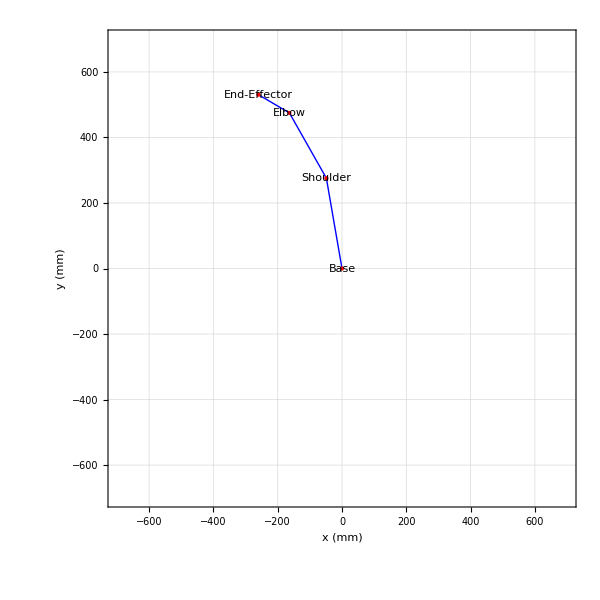

```mathematica
alignCenter@plotArm[100,20,30]
```

```mathematica
alignCenter@Manipulate[plotArm[θ1, θ2, θ3],{{θ1, 30, "θ1 (deg)"}, 79, 180, Appearance -> "Labeled"},{{θ2, 45, "θ2 (deg)"}, -θ2Max/2, θ2Max/2, Appearance -> "Labeled"},{{θ3, 20, "θ3 (deg)"}, -θ3Max/2, θ3Max/2, Appearance -> "Labeled"}]
```

## Topic 1: Numerical Differentiation

#### Why a 3 x3 Jacobian?

The Jacobian J of the forward kinematics links small joint - angle changes to small pose changes :
   
       Δpose ≃ J · Δθ

Since FK has 3 outputs (x, y, φ) and 3 inputs (θ1, θ2, θ3), J is a 3*3 matrix whose (i, j) entry is -Graphics- . Each column is the derivative of the full pose with respect to one angle . We compute each column numerically using finite - difference formulas from the course .

-Graphics-

#### Analytical Jacobian

```mathematica
ClearAll@jacobianAnalytical
jacobianAnalytical[θ1_,θ2_,θ3_]:=D[forwardKinematics[t1,t2,t3],{{t1,t2,t3}}]/. Thread[{t1,t2,t3}->{θ1,θ2,θ3}]
```

```mathematica
jacobianAnalytical[100,20,30]//N
```

{{-9.25779,-4.44511,-0.968658},{-4.5335,-3.68489,-1.67776},{1.,1.,1.}}

#### Method 1 : Forward Difference O (h)

Forward difference uses two evaluations: the current point and one step ahead. Truncation error is first order in h. Cheap but least accurate.

-Graphics-

```mathematica
jacobian=ResourceFunction["JacobianMatrix"]
```

```mathematica
partialRules={Derivative[1,0,0][f_][_,_,_]:>"\!\(\*FractionBox[\(∂\*SubscriptBox[\("<>ToString[f[[1]]]<>"\), \("<>ToString[f[[2]]]<>"\)]\), \(∂\*SubscriptBox[\(θ\), \(1\)]\)]\)",Derivative[0,1,0][f_][_,_,_]:>"\!\(\*FractionBox[\(∂\*SubscriptBox[\("<>ToString[f[[1]]]<>"\), \("<>ToString[f[[2]]]<>"\)]\), \(∂\*SubscriptBox[\(θ\), \(2\)]\)]\)",Derivative[0,0,1][f_][_,_,_]:>"\!\(\*FractionBox[\(∂\*SubscriptBox[\("<>ToString[f[[1]]]<>"\), \("<>ToString[f[[2]]]<>"\)]\), \(∂\*SubscriptBox[\(θ\), \(3\)]\)]\)"};
Style[J==MatrixForm[D[{Subscript[f,1][θ1,θ2,θ3],Subscript[f,2][θ1,θ2,θ3],Subscript[f,3][θ1,θ2,θ3]},{{θ1,θ2,θ3}}]/. partialRules],25]
```

J==((∂SubscriptBox[f, 1])/(∂SubscriptBox[θ, 1]) | (∂SubscriptBox[f, 1])/(∂SubscriptBox[θ, 2]) | (∂SubscriptBox[f, 1])/(∂SubscriptBox[θ, 3])
(∂SubscriptBox[f, 2])/(∂SubscriptBox[θ, 1]) | (∂SubscriptBox[f, 2])/(∂SubscriptBox[θ, 2]) | (∂SubscriptBox[f, 2])/(∂SubscriptBox[θ, 3])
(∂SubscriptBox[f, 3])/(∂SubscriptBox[θ, 1]) | (∂SubscriptBox[f, 3])/(∂SubscriptBox[θ, 2]) | (∂SubscriptBox[f, 3])/(∂SubscriptBox[θ, 3]))

```mathematica
jResource=jacobian[forwardKinematics[t1,t2,t3],{t1,t2,t3}]/. {t1->100,t2->20,t3->30}//N
```

{{-9.25779,-4.44511,-0.968658},{-4.5335,-3.68489,-1.67776},{1.,1.,1.}}

```mathematica
ClearAll@jacobianForward
jacobianForward[θ1_, θ2_, θ3_, h_: 0.01] :=Module[{f0, df1, df2, df3},
  f0  = forwardKinematics[θ1, θ2, θ3];
  df1 = (forwardKinematics[θ1 + h, θ2, θ3] - f0)/h;
  df2 = (forwardKinematics[θ1, θ2 + h, θ3] - f0)/h;
  df3 = (forwardKinematics[θ1, θ2, θ3 + h] - f0)/h;
  Transpose[{df1, df2, df3}]
]
```

```mathematica
jacobianAnalytical[100,20,30]//N
jacobianForward[100,20,30,0.01]
```

{{-9.25779,-4.44511,-0.968658},{-4.5335,-3.68489,-1.67776},{1.,1.,1.}}

{{-9.25739,-4.44478,-0.968511},{-4.53431,-3.68528,-1.67785},{1.,1.,1.}}

#### Method 2 : Centered Difference O (h^2)

Centered difference uses points on both sides of θ. The odd-order error terms cancel, leaving second-order accuracy. This is our default for Newton-Raphson because it is accurate and inexpensive.

																-Graphics-

```mathematica
ClearAll@jacobianCentered
jacobianCentered[θ1_, θ2_, θ3_, h_: 0.01] := Module[{df1, df2, df3},
  df1 = (forwardKinematics[θ1 + h, θ2, θ3] -
         forwardKinematics[θ1 - h, θ2, θ3])/(2 h);
  df2 = (forwardKinematics[θ1, θ2 + h, θ3] -
         forwardKinematics[θ1, θ2 - h, θ3])/(2 h);
  df3 = (forwardKinematics[θ1, θ2, θ3 + h] -
         forwardKinematics[θ1, θ2, θ3 - h])/(2 h);
  Transpose[{df1, df2, df3}]
]
```

```mathematica
jacobianAnalytical[100,20,30]//N
jacobianForward[100,20,30,0.01]
jacobianCentered[100,20,30,0.01]
```

{{-9.25779,-4.44511,-0.968658},{-4.5335,-3.68489,-1.67776},{1.,1.,1.}}

{{-9.25739,-4.44478,-0.968511},{-4.53431,-3.68528,-1.67785},{1.,1.,1.}}

{{-9.25779,-4.44511,-0.968658},{-4.5335,-3.68489,-1.67776},{1.,1.,1.}}

#### Method 3 : Centered Difference O (h^4)

A five-point stencil cancels higher-order error terms to give fourth-order accuracy. More function evaluations, much smaller truncation error.

-Graphics-

```mathematica
ClearAll@jacobianCentered4
jacobianCentered4[θ1_, θ2_, θ3_, h_: 0.01] :=Module[{df1, df2, df3},
  df1 = (-forwardKinematics[θ1 + 2 h, θ2, θ3] +
          8 forwardKinematics[θ1 + h, θ2, θ3] -
          8 forwardKinematics[θ1 - h, θ2, θ3] +
          forwardKinematics[θ1 - 2 h, θ2, θ3])/(12 h);
  df2 = (-forwardKinematics[θ1, θ2 + 2 h, θ3] +
          8 forwardKinematics[θ1, θ2 + h, θ3] -
          8 forwardKinematics[θ1, θ2 - h, θ3] +
          forwardKinematics[θ1, θ2 - 2 h, θ3])/(12 h);
  df3 = (-forwardKinematics[θ1, θ2, θ3 + 2 h] +
          8 forwardKinematics[θ1, θ2, θ3 + h] -
          8 forwardKinematics[θ1, θ2, θ3 - h] +
          forwardKinematics[θ1, θ2, θ3 - 2 h])/(12 h);
  Transpose[{df1, df2, df3}]
]
```

```mathematica
jExact=jacobianAnalytical[100,20,30]//N
jForward=jacobianForward[100,20,30,0.01]
jCentered=jacobianCentered[100,20,30,0.01]
jCentered4=jacobianCentered4[100,20,30,0.01]
jResource
```

{{-9.25779,-4.44511,-0.968658},{-4.5335,-3.68489,-1.67776},{1.,1.,1.}}

{{-9.25739,-4.44478,-0.968511},{-4.53431,-3.68528,-1.67785},{1.,1.,1.}}

{{-9.25779,-4.44511,-0.968658},{-4.5335,-3.68489,-1.67776},{1.,1.,1.}}

{{-9.25779,-4.44511,-0.968658},{-4.5335,-3.68489,-1.67776},{1.,1.,1.}}

{{-9.25779,-4.44511,-0.968658},{-4.5335,-3.68489,-1.67776},{1.,1.,1.}}

#### Comparison of Jacobian Methods

```mathematica
hValues=10.0^Range[0,-8,-1];
errForward=Table[Max[Abs[jacobianForward[100,20,30,hh]-jExact]],{hh,hValues}]
errCentered=Table[Max[Abs[jacobianCentered[100,20,30,hh]-jExact]],{hh,hValues}]
errCentered4=Table[Max[Abs[jacobianCentered4[100,20,30,hh]-jExact]],{hh,hValues}]
```

{0.0805572,0.00807664,0.000807871,0.0000807893,8.07897×10^-6,8.00173×10^-7,7.51525×10^-8,8.02598×10^-7,7.26406×10^-6}

{0.000470007,4.70014×10^-6,4.69954×10^-8,4.12184×10^-10,3.86299×10^-10,4.57814×10^-9,7.33707×10^-8,7.17546×10^-7,4.31331×10^-6}

{2.86338×10^-8,3.47988×10^-12,1.16298×10^-11,8.99316×10^-11,5.75777×10^-10,4.57814×10^-9,8.28446×10^-8,9.07024×10^-7,6.99137×10^-6}

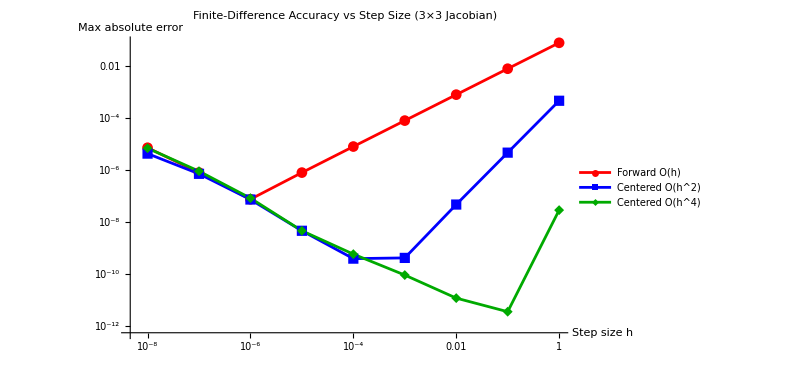

```mathematica
alignCenter@ListLogLogPlot[{Transpose[{hValues,errForward}],Transpose[{hValues,errCentered}],Transpose[{hValues,errCentered4}]},PlotLegends->{"Forward O(h)","Centered O(h^2)","Centered O(h^4)"},AxesLabel->{"Step size h","Max absolute error"},PlotLabel->"Finite-Difference Accuracy vs Step Size (3×3 Jacobian)",PlotStyle->{Red,Blue,Darker[Green]},Joined->True,PlotMarkers->Automatic,ImageSize->600]
```

## Topic 2: Linear Algebra (Gaussian Elimination, 3×3) & Topic 3 : Newton - Raphson for the 3x3 System

Each Newton - Raphson step requires solving the linear system

    J · δ = -f

where J is the 3x3 Jacobian, f the 3 - component residual vector, and δ the angle correction . We implement Gaussian elimination with partial pivoting .

```mathematica
ClearAll[gaussianEliminationPartialPivoting]
gaussianEliminationPartialPivoting[augMatr_]:=Module[{n,i,j,k,factor,x,maxRow,temp,Atemp=augMatr[[All,1;;-2]],btemp=augMatr[[All,-1]]},n=Length[btemp];

(*Forward elimination with partial pivoting*)
For[k=1,k<=n-1,k++,
(*Partial pivoting:Find row with largest absolute value in column k*)maxRow=First@Ordering[Abs[Atemp[[k;;,k]]],-1]+k-1;
(*Swap rows if necessary*)If[maxRow!=k,{Atemp[[k]],Atemp[[maxRow]]}={Atemp[[maxRow]],Atemp[[k]]};
{btemp[[k]],btemp[[maxRow]]}={btemp[[maxRow]],btemp[[k]]};];
(*Perform elimination to make the pivot element 1 and eliminate the column*)factor=Atemp[[k,k]];
If[factor!=0,Atemp[[k]]=Atemp[[k]]/factor;
btemp[[k]]=btemp[[k]]/factor;];
(*Eliminate the k-th column in all other rows*)
For[i=k+1,i<=n,i++,factor=Atemp[[i,k]];
Atemp[[i]]=Atemp[[i]]-factor*Atemp[[k]];
btemp[[i]]=btemp[[i]]-factor*btemp[[k]];];];

(*Back substitution*)x=Table[0,{n}];
x[[n]]=btemp[[n]]/Atemp[[n,n]];
For[i=n-1,i>=1,i--,x[[i]]=(btemp[[i]]-Total[Atemp[[i,i+1;;n]]*x[[i+1;;n]]])/Atemp[[i,i]];];
(*Return the solution vector*)x]
```

The 3-DOF IK is the root of the vector-valued function

    f(θ1, θ2, θ3) = FK(θ1, θ2, θ3) - (xTarget, yTarget, φTarget)

Newton-Raphson for systems: linearise at the current guess, solve for the correction, update:

    {θ1, θ2, θ3}_{n+1} = {θ1, θ2, θ3}_n + δ,   with   J · δ = -f

The per-iteration cost is: (a) evaluate f via FK, (b) build J using centered finite differences (Topic 1), (c) solve J · δ = -f via Gaussian elimination (Topic 2). All three course topics appear in each step.

```mathematica
ClearAll@newtonIKStep
newtonIKStep[xTarget_, yTarget_, φTarget_][{θ1_, θ2_, θ3_}] := Module[{f, J, augMat, δ},
  f = forwardKinematics[θ1, θ2, θ3] - {xTarget, yTarget, φTarget};
  J = jacobianCentered[θ1, θ2, θ3];
  augMat = MapThread[Append, {J, -f}];
  δ = gaussianEliminationPartialPivoting[augMat];
  {θ1 + δ[[1]], θ2 + δ[[2]], θ3 + δ[[3]]}
  ]
```

```mathematica
newtonIKStep[-200,400,90][{100,40,-30}]
```

{64.6879,130.956,-105.644}

```mathematica
forwardKinematics[64.68791827937113,130.95621094520294,-105.64412922448476]
```

{-101.766,302.096,90.}

```mathematica
ClearAll@residual
residual[θ_]:=Norm[(forwardKinematics@@θ)-{-200.,400.,90.}//N];
```

```mathematica
trajectory1=NestWhileList[newtonIKStep[-200.,400.,90.],{100.,40.,-30.},residual[#]>10^-4&,1,50]
```

{{100.,40.,-30.},{64.6879,130.956,-105.644},{83.1653,97.1388,-90.3041},{83.8376,93.5221,-87.3597},{83.8995,93.4626,-87.3621},{83.8995,93.4625,-87.3621}}

```mathematica
Length[trajectory1]
```

6

```mathematica
Last[trajectory1]
```

{83.8995,93.4625,-87.3621}

```mathematica
forwardKinematics[Last[trajectory1][[1]],Last[trajectory1][[2]],Last[trajectory1][[3]]]//N
```

{-200.,400.,90.}

```mathematica
residual[Last[trajectory1]]
```

5.85257×10^-11

5.85257×10^-11

5.85257×10^-11

«1 more identical outputs»

```mathematica
residuals=Norm[forwardKinematics[#[[1]],#[[2]],#[[3]]]-{-200.,400.,90.}]&/@trajectory1;
```

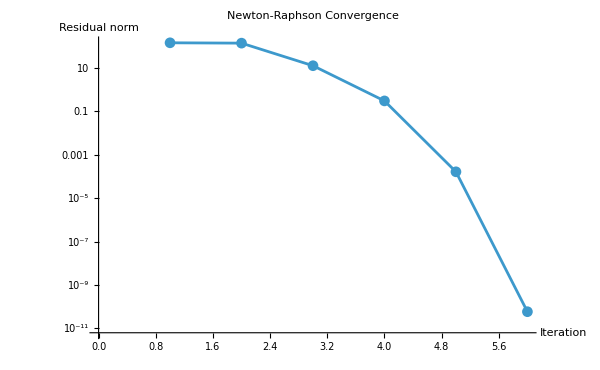

```mathematica
alignCenter@ListLogPlot[residuals,Joined->True,PlotMarkers->Automatic,AxesLabel->{"Iteration","Residual norm"},PlotLabel->"Newton-Raphson Convergence",ImageSize->600]
```

```mathematica
ClearAll[inverseKinematics]
inverseKinematics[xTarget_,yTarget_,φTarget_,θ1init_,θ2init_,θ3init_,maxIter_]:=NestList[newtonIKStep[xTarget,yTarget,φTarget],{θ1init,θ2init,θ3init},maxIter]
```

```mathematica
inverseKinematics[-200,400,90,100,40,-30,10]
```

{{100,40,-30},{64.6879,130.956,-105.644},{83.1653,97.1388,-90.3041},{83.8376,93.5221,-87.3597},{83.8995,93.4626,-87.3621},{83.8995,93.4625,-87.3621},{83.8995,93.4625,-87.3621},{83.8995,93.4625,-87.3621},{83.8995,93.4625,-87.3621},{83.8995,93.4625,-87.3621},{83.8995,93.4625,-87.3621}}

## Interactive IK (3-DOF)

Now we can drag the sliders to choose a target pose (xTarget, yTarget, φTarget) and an initial guess. The widget runs the full 3×3 Newton-Raphson IK, reports the solved angles and the residual norm, and draws the resulting arm configuration.

```mathematica
alignCenter@Manipulate[Module[{target,res,θ1s,θ2s,θ3s,fk,armPlot,errNorm},target={xT,yT,φT};
res=inverseKinematics[xT,yT,φT,θ1g,θ2g,θ3g,nIter];
θ1s=res[[-1,1]];θ2s=res[[-1,2]];θ3s=res[[-1,3]];
fk=forwardKinematics[θ1s,θ2s,θ3s]//N;
errNorm=Norm[fk-target];
armPlot=plotArm[θ1s,θ2s,θ3s];
armPlot],
{{xT,292.3,"x target (mm)"},-600,600,1,Appearance->"Labeled"},{{yT,472.7,"y target (mm)"},-600,600,1,Appearance->"Labeled"},{{φT,95.0,"φ target (deg)"},-180,180,1,Appearance->"Labeled"},Delimiter,{{θ1g,10.0,"θ1 guess (deg)"},-70,70,1,Appearance->"Labeled"},{{θ2g,10.0,"θ2 guess (deg)"},-100,100,1,Appearance->"Labeled"},{{θ3g,10.0,"θ3 guess (deg)"},-95,95,1,Appearance->"Labeled"},Delimiter,{{nIter,15,"Max iterations"},1,30,1,Appearance->"Labeled"}]
```

## Conclusion

This report implemented inverse kinematics for a 3-link planar model of the SCORBOT-ER9Pro using three course topics. Numerical differentiation (centered finite differences) builds the Jacobian at each step; Gaussian elimination with partial pivoting solves the resulting linear system; Newton-Raphson iterates to convergence. The solver reached residual norm below 10^-10 in 6 iterations, demonstrating quadratic convergence characteristic of Newton-Raphson methods.

## Thank you!

### Questions? :)

```mathematica
alignCenter=Function[arg,Pane[arg,Full,Alignment->Center]];
```